### Start choosing the example:

```mathematica
t=17;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Get::noopen: Cannot open /Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m.

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,I1}},Exit Vertices and Terminal Costs→{{1,U1},{3,U2}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,U1->0,U2->3,S1->1,S2->0}];//Timing
MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[j90]&&NonNegative[1-j90]&&NonNegative[1-j90]&&NonNegative[j90]&&NonNegative[j90]&&NonNegative[j90]&&NonNegative[1-j90]&&NonNegative[1-j90]&&NonNegative[-u109]&&NonNegative[1-j90-u109+u111]&&NonNegative[j90+u109-u111]&&NonNegative[j90+u109-u113]&&NonNegative[u111-u113]&&NonNegative[4-j90-u111]&&(j90==0||-u109==0)&&(j90==0||j90+u109-u113==0)&&(1-j90==0||u111-u113==0)&&(1-j90==0||4-j90-u111==0)
and the rules are:
<|j93→1,u115→0,u117→3,j89→0,j91→1-j90,j92→1-j90,j94→j90,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→j90,jt106→1-j90,jt107→1-j90,jt108→0,jt99→j90,u110→0,u112→3,u114→j90+u109,u116→-1+j90+u111,u118→u113|>

DataToEquations: The system is:
j90==1&&u109==0&&u111==1&&u113==1
and the rules are:
<|j93→1,u115→0,u117→3,j89→0,j91→1-j90,j92→1-j90,j94→j90,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→j90,jt106→1-j90,jt107→1-j90,jt108→0,jt99→j90,u110→0,u112→3,u114→j90+u109,u116→-1+j90+u111,u118→u113|>

DataToEquations: It took 0.034572 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.057104,Null}

<|{1,1->2}→0,{1,1->ex87}→0,{2,1->2}→1,{2,2->3}→1,{2,en86->2}→1,{3,2->3}→1,{3,3->ex88}→3,{en86,en86->2}→1,{ex87,1->ex87}→0,{ex88,3->ex88}→3|>

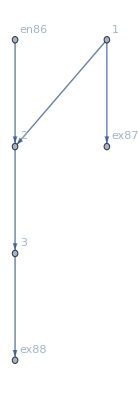

<|{1,1->2}→u506,{1,en479->1}→u506,{2,1->2}→-1+u506,{2,2->3}→u507,{2,2->4}→u508,{3,2->3}→-1+j484+u507,{3,3->ex480}→5,{4,2->4}→-j484+u508,{4,4->ex481}→1,{en479,en479->1}→u506,{ex480,3->ex480}→5,{ex481,4->ex481}→1|>

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j93→1,u115→0,u117→3,j89→0,j91→0,j92→0,j94→1,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1,jt106→0,jt107→0,jt108→0,jt99→1,u110→0,u112→3,u114→1,u116→1,u118→1,j90→1,u109→0,u111→1,u113→1|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j89→0,j90→1.,j91→0.,j92→0.,j93→1,j94→1.,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1.,jt106→0.,jt107→0.,jt108→0,jt99→1.,u109→0,u110→0,u111→0.705756,u112→3,u113→0.705756,u114→0.705756,u115→0,u116→0.705756,u117→3,u118→0.705756|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j89→0,j90→1.,j91→0.,j92→0.,j93→1,j94→1.,j95→0,j96→0,j97→0,j98→0,jt100→0,jt101→0,jt102→0,jt103→0,jt104→0,jt105→1.,jt106→0.,jt107→0.,jt108→0,jt99→1.,u109→0,u110→0,u111→0.72685,u112→3,u113→0.72685,u114→0.72685,u115→0,u116→0.72685,u117→3,u118→0.72685|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[0.116271 √(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2),√(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2),(√(0.+Abs[-6.93911+1. j51-IntM[10-j51]]^2+Abs[3.06089-1. j51-IntM[j51]]^2))/(√(55.232+Abs[10-j51+IntM[10-j51]]^2+Abs[j51+IntM[j51]]^2))]

ReplaceAll::reps: {u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51] is not a list, Rule, or Association.

ReplaceAll::reps: {u75==u76&&10-u74+u80==7.43182&&j51-u75+u81==j51+IntM[j51]&&10-j51-u76+u82==10-j51+IntM[10-j51]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```